```mathematica
Chebyshev[f_,x_,n_]:=Module[{mk,c},
mk=Table[N@Cos[(π m(k+1/2))/n],{m,0,n-1},{k,0,n-1}];
c=f/@mk[[2]];
c=2mk.c/n;
c.Table[ChebyshevT[k,x],{k,0,n-1}]-c[[1]]/2
]
```

```mathematica
f[x_]:=Sin[10x];
```

```mathematica
Chebyshev[f,x,10]//Simplify
```

4.996×10^-17+9.05386 x-1.31006×10^-15 x^2-118.399 x^3+5.15143×10^-15 x^4+406.223 x^5-6.75016×10^-15 x^6-509.495 x^7+2.84217×10^-15 x^8+212.466 x^9

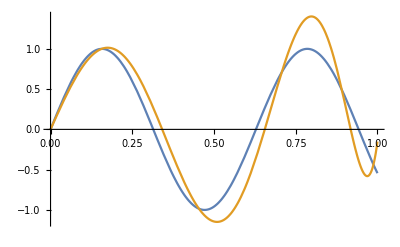

```mathematica
Plot[{f[x],Chebyshev[f,x,10]}//Evaluate,{x,0,1}]
```